OWNER OF THE FILE
NAME:- PARTH KUMAR SINGH
COURSE:- B.Sc(Hons.) MATHEMATICS
ROLL NO:- 2232139

PRACTICAL 1 :- BISECTION METHOD

Ques.1 :- Perform 10 iterations of Bisection Method to find the root of the function f(x) = x^3-5x+1 in the interval [0,1]

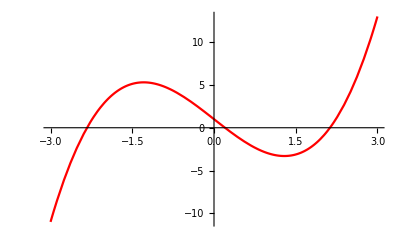

i | a_i | p_i | b_i | f[p_i]
1. | 0. | 0.5 | 1. | -1.375
2. | 0. | 0.25 | 0.5 | -0.234375
3. | 0. | 0.125 | 0.25 | 0.37695313
4. | 0.125 | 0.1875 | 0.25 | 0.069091797
5. | 0.1875 | 0.21875 | 0.25 | -0.083282471
6. | 0.1875 | 0.203125 | 0.21875 | -0.0072441101
7. | 0.1875 | 0.1953125 | 0.203125 | 0.030888081
8. | 0.1953125 | 0.19921875 | 0.203125 | 0.011812866
9. | 0.19921875 | 0.20117188 | 0.203125 | 0.0022820756
10. | 0.20117188 | 0.20214844 | 0.203125 | -0.0024815956

Root After 10 iterations 0.20214844

```mathematica
f[x_]:=x^3-5x+1;
Plot[f[x],{x,-3,3},PlotStyle->Red]
a=0;
b=1;
n=10;
If[f[a]*f[b]>0,Print["We cannot continue with the Bisection Method."],i=1;p=(a+b)/2;OutputDetails={{i,a,p,b,f[p]}};
While[i<n,If[Sign[f[a]]==Sign[f[p]],a=p,b=p];p=(a+b)/2;i++;OutputDetails=Append[OutputDetails,{i,a,p,b,f[p]}];]]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","a_i","p_i","b_i","f[p_i]"}}]],8]];(*Printing Table*)
Print["Root After ",n," iterations ",NumberForm[N[p],8]]
(*8 is used to give the result with 8 digits precision*)
```

Ques.2 :- Perform 10 iterations of Bisection Method to find the root of the function f(x) = Cosx-x=0 in the interval [0,1]

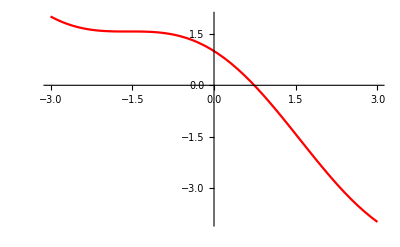

i | a_i | p_i | b_i | f[p_i]
1. | 0. | 0.5 | 1. | 0.37758256
2. | 0.5 | 0.75 | 1. | -0.018311131
3. | 0.5 | 0.625 | 0.75 | 0.18596312
4. | 0.625 | 0.6875 | 0.75 | 0.085334946
5. | 0.6875 | 0.71875 | 0.75 | 0.033879372
6. | 0.71875 | 0.734375 | 0.75 | 0.0078747255
7. | 0.734375 | 0.7421875 | 0.75 | -0.0051957117
8. | 0.734375 | 0.73828125 | 0.7421875 | 0.0013451498
9. | 0.73828125 | 0.74023438 | 0.7421875 | -0.0019238728
10. | 0.73828125 | 0.73925781 | 0.74023438 | -0.00028900915

Root After 10 iterations 0.73925781

```mathematica
f[x_]:=Cos[x]-x;
Plot[f[x],{x,-3,3},PlotStyle->Red]
a=0;
b=1;
n=10;
If[f[a]*f[b]>0,Print["We cannot continue with the Bisection Method."],i=1;p=(a+b)/2;OutputDetails={{i,a,p,b,f[p]}};
While[i<n,If[Sign[f[a]]==Sign[f[p]],a=p,b=p];p=(a+b)/2;i++;OutputDetails=Append[OutputDetails,{i,a,p,b,f[p]}];]]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","a_i","p_i","b_i","f[p_i]"}}]],8]];(*Printing Table*)
Print["Root After ",n," iterations ",NumberForm[N[p],8]]
(*8 is used to give the result with 8 digits precision*)
```

Ques.3 :- Perform 10 iterations of Bisection Method to find the root of the function f(x) = e^x-x=0 in the interval [0,1]

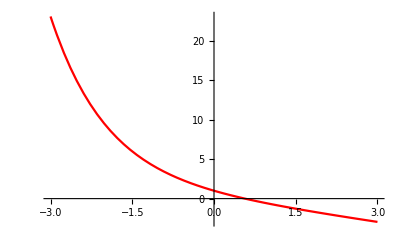

i | a_i | p_i | b_i | f[p_i]
1. | 0. | 0.5 | 1. | 0.10653066
2. | 0.5 | 0.75 | 1. | -0.27763345
3. | 0.5 | 0.625 | 0.75 | -0.089738571
4. | 0.5 | 0.5625 | 0.625 | 0.0072828247
5. | 0.5625 | 0.59375 | 0.625 | -0.04149755
6. | 0.5625 | 0.578125 | 0.59375 | -0.017175839
7. | 0.5625 | 0.5703125 | 0.578125 | -0.0049637604
8. | 0.5625 | 0.56640625 | 0.5703125 | 0.001155202
9. | 0.56640625 | 0.56835938 | 0.5703125 | -0.0019053596
10. | 0.56640625 | 0.56738281 | 0.56835938 | -0.00037534917

Root After 10 iterations 0.56738281

```mathematica
f[x_]:=Exp[-x]-x;
Plot[f[x],{x,-3,3},PlotStyle->Red]
a=0;
b=1;
n=10;
If[f[a]*f[b]>0,Print["We cannot continue with the Bisection Method."],i=1;p=(a+b)/2;OutputDetails={{i,a,p,b,f[p]}};
While[i<n,If[Sign[f[a]]==Sign[f[p]],a=p,b=p];p=(a+b)/2;i++;OutputDetails=Append[OutputDetails,{i,a,p,b,f[p]}];]]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","a_i","p_i","b_i","f[p_i]"}}]],8]];(*Printing Table*)
Print["Root After ",n," iterations ",NumberForm[N[p],8]]
(*8 is used to give the result with 8 digits precision*)
```

Ques.4:- Perform 10 iterations of Bisection Method to find the root of the function f(x) = ln(1+x)-cosx=0 in the interval [0,1]

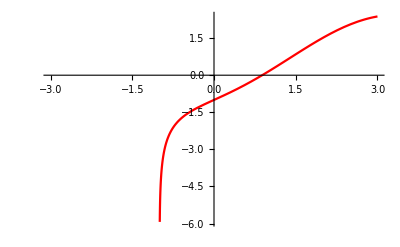

i | a_i | p_i | b_i | f[p_i]
1. | 0. | 0.5 | 1. | -0.47211745
2. | 0.5 | 0.75 | 1. | -0.17207308
3. | 0.75 | 0.875 | 1. | -0.012388199
4. | 0.875 | 0.9375 | 1. | 0.069593407
5. | 0.875 | 0.90625 | 0.9375 | 0.028435895
6. | 0.875 | 0.890625 | 0.90625 | 0.0079812284
7. | 0.875 | 0.8828125 | 0.890625 | -0.0022142544
8. | 0.8828125 | 0.88671875 | 0.890625 | 0.0028808088
9. | 0.8828125 | 0.88476563 | 0.88671875 | 0.00033260588
10. | 0.8828125 | 0.88378906 | 0.88476563 | -0.00094099231

Root After 10 iterations 0.88378906

```mathematica
f[x_]:=Log[1+x]-Cos[x];
Plot[f[x],{x,-3,3},PlotStyle->Red]
a=0;
b=1;
n=10;
If[f[a]*f[b]>0,Print["We cannot continue with the Bisection Method."],i=1;p=(a+b)/2;OutputDetails={{i,a,p,b,f[p]}};
While[i<n,If[Sign[f[a]]==Sign[f[p]],a=p,b=p];p=(a+b)/2;i++;OutputDetails=Append[OutputDetails,{i,a,p,b,f[p]}];]]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","a_i","p_i","b_i","f[p_i]"}}]],8]];(*Printing Table*)
Print["Root After ",n," iterations ",NumberForm[N[p],8]]
(*8 is used to give the result with 8 digits precision*)
```

Ques.5:- Perform 10 iterations of Bisection Method to find the root of the function cube root of 17 in the interval [0,1]

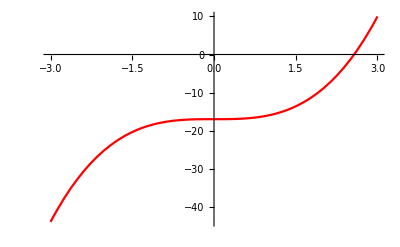

i | a_i | p_i | b_i | f[p_i]
1. | 2. | 2.5 | 3. | -1.375
2. | 2.5 | 2.75 | 3. | 3.796875
3. | 2.5 | 2.625 | 2.75 | 1.0878906
4. | 2.5 | 2.5625 | 2.625 | -0.17358398
5. | 2.5625 | 2.59375 | 2.625 | 0.44955444
6. | 2.5625 | 2.578125 | 2.59375 | 0.13609695
7. | 2.5625 | 2.5703125 | 2.578125 | -0.019214153
8. | 2.5703125 | 2.5742188 | 2.578125 | 0.058323562
9. | 2.5703125 | 2.5722656 | 2.5742188 | 0.019525267
10. | 2.5703125 | 2.5712891 | 2.5722656 | 0.00014820043

Root After 10 iterations 2.5712891

```mathematica
f[x_]:=x^3-17;
Plot[f[x],{x,-3,3},PlotStyle->Red]
a=2;
b=3;
n=10;
If[f[a]*f[b]>0,Print["We cannot continue with the Bisection Method."],i=1;p=(a+b)/2;OutputDetails={{i,a,p,b,f[p]}};
While[i<n,If[Sign[f[a]]==Sign[f[p]],a=p,b=p];p=(a+b)/2;i++;OutputDetails=Append[OutputDetails,{i,a,p,b,f[p]}];]]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","a_i","p_i","b_i","f[p_i]"}}]],8]];(*Printing Table*)
Print["Root After ",n," iterations ",NumberForm[N[p],8]]
(*8 is used to give the result with 8 digits precision*)
```

Ques.6:- Perform 10 iterations of Bisection Method to find the root of the function approximate value of 1/37 in the interval [0,1]

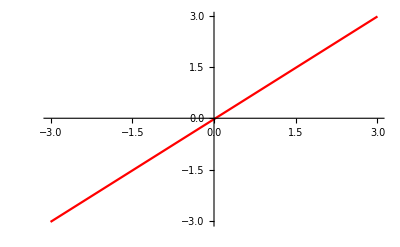

i | a_i | p_i | b_i | f[p_i]
1. | -1. | 0. | 1. | -0.027027027
2. | 0. | 0.5 | 1. | 0.47297297
3. | 0. | 0.25 | 0.5 | 0.22297297
4. | 0. | 0.125 | 0.25 | 0.097972973
5. | 0. | 0.0625 | 0.125 | 0.035472973
6. | 0. | 0.03125 | 0.0625 | 0.004222973
7. | 0. | 0.015625 | 0.03125 | -0.011402027
8. | 0.015625 | 0.0234375 | 0.03125 | -0.003589527
9. | 0.0234375 | 0.02734375 | 0.03125 | 0.00031672297
10. | 0.0234375 | 0.025390625 | 0.02734375 | -0.001636402

Root After 10 iterations 0.025390625

```mathematica
f[x_]:=x-1/37;
Plot[f[x],{x,-3,3},PlotStyle->Red]
a=-1;
b=1;
n=10;
If[f[a]*f[b]>0,Print["We cannot continue with the Bisection Method."],i=1;p=(a+b)/2;OutputDetails={{i,a,p,b,f[p]}};
While[i<n,If[Sign[f[a]]==Sign[f[p]],a=p,b=p];p=(a+b)/2;i++;OutputDetails=Append[OutputDetails,{i,a,p,b,f[p]}];]]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","a_i","p_i","b_i","f[p_i]"}}]],8]];(*Printing Table*)
Print["Root After ",n," iterations ",NumberForm[N[p],8]]
(*8 is used to give the result with 8 digits precision*)
```

PRACTICAL 2 :- NEWTON RAPHSON METHOD

Ques. 1: Find the root of the function f(x)= x^3-5x+1. Perform 5 iterations of Newton Raphson Method to find the root of the function starting with the initial approximation 0.5.

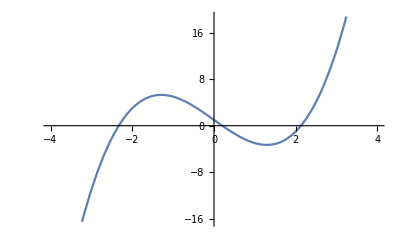

```mathematica
Clear[x,f,a,b,m,n,i]
f[x_]:=x^3-5x+1;
Plot[f[x],{x,-4,4}]
```

```mathematica
ClearAll;
```

```mathematica
k=0.5;(*k = Subscript[p, o]*)
n=5;
If[f'[k]==0,
Print["We cannot continue with the Newton Raphson Mehtod"],
i=1;
p=k-f[k]/f'[k];(*k = Subscript[p, n-1]*)
OutputDetails={{i,k}};
While[i<n,p=k-f[k]/f'[k];k=p;i++;
OutputDetails=Append[OutputDetails,{i,k}];]]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","k_i"}}]],8]];
(*Printing Table*)
Print["Root after ",n," iterations ",NumberForm[N[k],8]]
(*8 is used to give the result with 8 digits precision*)
```

i | k_i
1. | 0.5
2. | 0.17647059
3. | 0.20156807
4. | 0.20163968
5. | 0.20163968

Root after 5 iterations 0.20163968

Ques 2: Find the root of the function f(x)= x^3-17. Perform 5 iterations of Newton Raphson Method to find the root of the function starting with the initial approximation 2.

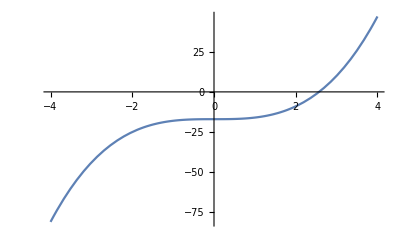

```mathematica
Clear[x,f,a,b,m,n,i]
f[x_]:=x^3-17;
Plot[f[x],{x,-4,4}]
```

```mathematica
ClearAll;
```

```mathematica
f[x_]:=x^3-17
```

```mathematica
k=2;(*k = Subscript[p, o]*)
n=5;
If[f'[k]==0,
Print["We cannot continue with the Newton Raphson Mehtod"],
i=1;
p=k-f[k]/f'[k];(*k = Subscript[p, n-1]*)
OutputDetails={{i,k}};
While[i<n,p=k-f[k]/f'[k];k=p;i++;
OutputDetails=Append[OutputDetails,{i,k}];]]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","k_i"}}]],8]];
(*Printing Table*)
Print["Root after ",n," iterations ",NumberForm[N[k],8]]
(*8 is used to give the result with 8 digits precision*)
```

i | k_i
1. | 2.
2. | 2.75
3. | 2.5826446
4. | 2.5713315
5. | 2.5712816

Root after 5 iterations 2.5712816

Ques 3: Find the root of the function f(x)=e^-x-x. Perform 5 iterations of Newton Raphson Method to find the root of the function starting with the initial approximation 0.5.

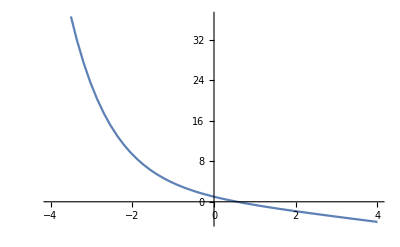

```mathematica
Clear[x,f,a,b,m,n,i]
f[x_]:=Exp[-x]-x;
Plot[f[x],{x,-4,4}]
```

```mathematica
k=0.5;(*k = Subscript[p, o]*)
n=5;
If[f'[k]==0,
Print["We cannot continue with the Newton Raphson Mehtod"],
i=1;
p=k-f[k]/f'[k];(*k = Subscript[p, n-1]*)
OutputDetails={{i,k}};
While[i<n,p=k-f[k]/f'[k];k=p;i++;
OutputDetails=Append[OutputDetails,{i,k}];]]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","k_i"}}]],8]];
(*Printing Table*)
Print["Root after ",n," iterations ",NumberForm[N[k],8]]
(*8 is used to give the result with 8 digits precision*)
```

i | k_i
1. | 0.5
2. | 0.566311
3. | 0.56714317
4. | 0.56714329
5. | 0.56714329

Root after 5 iterations 0.56714329

Ques 4: Find the root of the function f(x)=cosx-x. Perform 5 iterations of Newton Raphson Method to find the root of the function starting with the initial approximation 0.75.

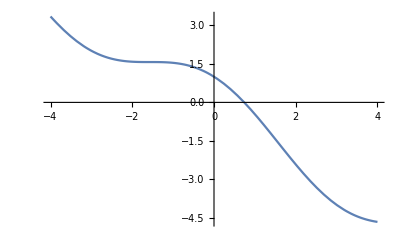

```mathematica
Clear[x,f,a,b,m,n,i]
f[x_]:=Cos[x]-x;
Plot[f[x],{x,-4,4}]
```

```mathematica
k=0.75;(*k = Subscript[p, o]*)
n=5;
If[f'[k]==0,
Print["We cannot continue with the Newton Raphson Mehtod"],
i=1;
p=k-f[k]/f'[k];(*k = Subscript[p, n-1]*)
OutputDetails={{i,k}};
While[i<n,p=k-f[k]/f'[k];k=p;i++;
OutputDetails=Append[OutputDetails,{i,k}];]]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","k_i"}}]],8]];
(*Printing Table*)
Print["Root after ",n," iterations ",NumberForm[N[k],8]]
(*8 is used to give the result with 8 digits precision*)
```

i | k_i
1. | 0.75
2. | 0.73911114
3. | 0.73908513
4. | 0.73908513
5. | 0.73908513

Root after 5 iterations 0.73908513

Ques 4: Find the root of the function f(x)=ln(1+x)-x. Perform 5 iterations of Newton Raphson Method to find the root of the function starting with the initial approximation 0.5.

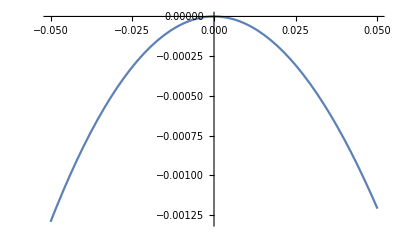

```mathematica
Clear[x,f,a,b,m,n,i]
f[x_]:=Log[1+x]-x;
Plot[f[x],{x,-0.05,0.05}]
```

```mathematica
k=0.5;(*k = Subscript[p, o]*)
n=10;
If[f'[k]==0,
Print["We cannot continue with the Newton Raphson Mehtod"],
i=1;
p=k-f[k]/f'[k];(*k = Subscript[p, n-1]*)
OutputDetails={{i,k}};
While[i<n,p=k-f[k]/f'[k];k=p;i++;
OutputDetails=Append[OutputDetails,{i,k}];]]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","k_i"}}]],8]];
(*Printing Table*)
Print["Root after ",n," iterations ",NumberForm[N[k],8]]
(*8 is used to give the result with 8 digits precision*)
```

i | k_i
1. | 0.5
2. | 0.21639532
3. | 0.10114167
4. | 0.048947214
5. | 0.024083797
6. | 0.011946374
7. | 0.0059495423
8. | 0.0029688891
9. | 0.0014829777
10. | 0.00074112258

Root after 10 iterations 0.00074112258

Ques 5: Find the root of the function f(x)=x^3+2 x^2-3x-1. Perform 5 iterations of Newton Raphson Method to find the root of the function starting with the initial approximation 0.75.

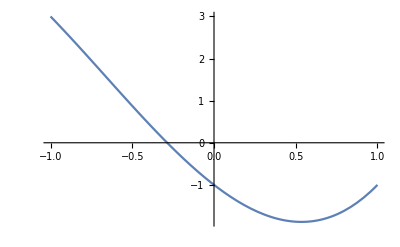

```mathematica
Clear[x,f,a,b,m,n,i]
f[x_]:=x^3+2 x^2-3x-1;
Plot[f[x],{x,-1,1}]
```

```mathematica
k=-0.25;(*k = Subscript[p, o]*)
n=5;
If[f'[k]==0,
Print["We cannot continue with the Newton Raphson Mehtod"],
i=1;
p=k-f[k]/f'[k];(*k = Subscript[p, n-1]*)
OutputDetails={{i,k}};
While[i<n,p=k-f[k]/f'[k];k=p;i++;
OutputDetails=Append[OutputDetails,{i,k}];]]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","k_i"}}]],8]];
(*Printing Table*)
Print["Root after ",n," iterations ",NumberForm[N[k],8]]
(*8 is used to give the result with 8 digits precision*)
```

i | k_i
1. | -0.25
2. | -0.28688525
3. | -0.28646212
4. | -0.28646207
5. | -0.28646207

Root after 5 iterations -0.28646207

PRACTICAL 3:- SECANT METHOD

Ques. 1: Find the root of the function f(x)=x^3-5x+1. Perform 6 iterations of Secant Method to find the root of the function starting with the initial approximation 0 and 1

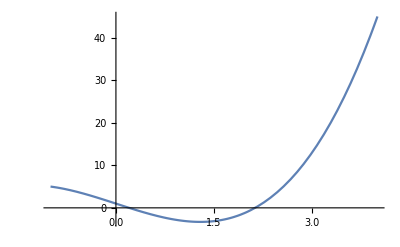

```mathematica
Clear[x,f,a,b,m,n,i]
f[x_]:=x^3-5x+1;
Plot[f[x],{x,-1,4}]
```

```mathematica
k=0 ; m=1;(*k = Subscript[p, o] and m = Subscript[p, 1]*)
n=6;
i=1;
p=m-f[m](m-k)/(f[m]-f[k]);(*k = Subscript[p, n-1] and m = Subscript[p, n]*)
OutputDetails={{i,p,f[p]}};
While[i<n,p=m-f[m](m-k)/(f[m]-f[k]);k=m;m=p;i++;OutputDetails=Append[OutputDetails,{i,p,f[p]}];]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","p_i","f[p_i]"}}]],8]];
(*Printing Table*)
Print["Root After ",n," iterations ",NumberForm[N[p],8]]
(*8 is used to give the result with 8 digits precision*)
```

i | p_i | f[p_i]
1. | 0.25 | -0.234375
2. | 0.25 | -0.234375
3. | 0.18644068 | 0.074277312
4. | 0.20173626 | -0.00047111617
5. | 0.20163985 | -8.642293×10^-7
6. | 0.20163968 | 1.0352523×10^-11

Root After 6 iterations 0.20163968

Ques. 2: Find the root of the function f(x)=e^-x-x. Perform 6 iterations of Secant Method to find the root of the function starting with the initial approximation 0 and 1

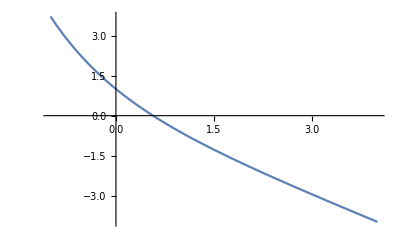

```mathematica
Clear[x,f,a,b,m,n,i]
f[x_]:=Exp[-x]-x;
Plot[f[x],{x,-1,4}]
```

```mathematica
k=0 ; m=1;(*k = Subscript[p, o] and m = Subscript[p, 1]*)
n=6;
i=1;
p=m-f[m](m-k)/(f[m]-f[k]);(*k = Subscript[p, n-1] and m = Subscript[p, n]*)
OutputDetails={{i,p,f[p]}};
While[i<n,p=m-f[m](m-k)/(f[m]-f[k]);k=m;m=p;i++;OutputDetails=Append[OutputDetails,{i,p,f[p]}];]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","p_i","f[p_i]"}}]],8]];
(*Printing Table*)
Print["Root After ",n," iterations ",NumberForm[N[p],8]]
(*8 is used to give the result with 8 digits precision*)
```

i | p_i | f[p_i]
1. | 0.61269984 | -0.070813948
2. | 0.61269984 | -0.070813948
3. | 0.56383839 | 0.0051823545
4. | 0.56717036 | -0.000042419242
5. | 0.56714331 | -2.5380167×10^-8
6. | 0.56714329 | 1.2423092×10^-13

Root After 6 iterations 0.56714329

Ques. 3: Find the root of the function f(x)=Cosx-x. Perform 6 iterations of Secant Method to find the root of the function starting with the initial approximation 0 and 1

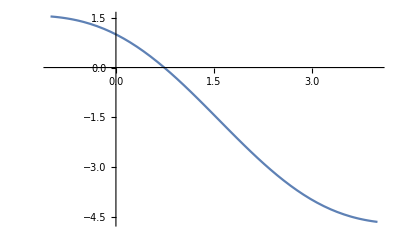

```mathematica
Clear[x,f,a,b,m,n,i]
f[x_]:=Cos[x]-x;
Plot[f[x],{x,-1,4}]
```

```mathematica
k=0 ; m=1;(*k = Subscript[p, o] and m = Subscript[p, 1]*)
n=6;
i=1;
p=m-f[m](m-k)/(f[m]-f[k]);(*k = Subscript[p, n-1] and m = Subscript[p, n]*)
OutputDetails={{i,p,f[p]}};
While[i<n,p=m-f[m](m-k)/(f[m]-f[k]);k=m;m=p;i++;OutputDetails=Append[OutputDetails,{i,p,f[p]}];]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","p_i","f[p_i]"}}]],8]];
(*Printing Table*)
Print["Root After ",n," iterations ",NumberForm[N[p],8]]
(*8 is used to give the result with 8 digits precision*)
```

i | p_i | f[p_i]
1. | 0.68507336 | 0.089299276
2. | 0.68507336 | 0.089299276
3. | 0.736299 | 0.004660039
4. | 0.73911936 | -0.000057285991
5. | 0.73908511 | 3.5292623×10^-8
6. | 0.73908513 | 2.6678659×10^-13

Root After 6 iterations 0.73908513

Ques. 4: Find the root of the function f(x)=ln(1+x)-x. Perform 6 iterations of Secant Method to find the root of the function starting with the initial approximation 0.1 and 1

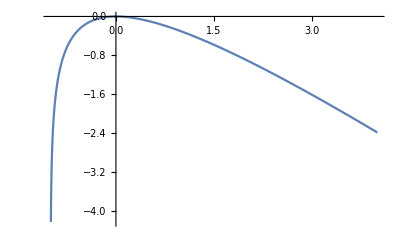

```mathematica
Clear[x,f,a,b,m,n,i]
f[x_]:=Log[1+x]-x;
Plot[f[x],{x,-1,4}]
```

```mathematica
k=0.1; m=1;(*k = Subscript[p, o] and m = Subscript[p, 1]*)
n=6;
i=1;
p=m-f[m](m-k)/(f[m]-f[k]);(*k = Subscript[p, n-1] and m = Subscript[p, n]*)
OutputDetails={{i,p,f[p]}};
While[i<n,p=m-f[m](m-k)/(f[m]-f[k]);k=m;m=p;i++;OutputDetails=Append[OutputDetails,{i,p,f[p]}];]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","p_i","f[p_i]"}}]],8]];
(*Printing Table*)
Print["Root After ",n," iterations ",NumberForm[N[p],8]]
(*8 is used to give the result with 8 digits precision*)
```

i | p_i | f[p_i]
1. | 0.086031254 | -0.0035012539
2. | 0.086031254 | -0.0035012539
3. | 0.075482317 | -0.002713089
4. | 0.039169855 | -0.00074767693
5. | 0.025355963 | -0.00031612973
6. | 0.015236603 | -0.00011491126

Root After 6 iterations 0.015236603

Ques. 5: Find the root of the function f(x)=x^3-17. Perform 6 iterations of Secant Method to find the root of the function starting with the initial approximation 0 and 1

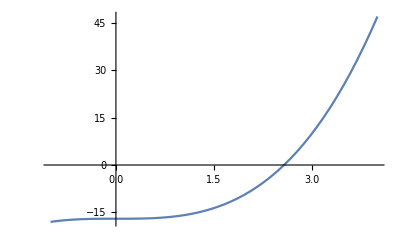

```mathematica
Clear[x,f,a,b,m,n,i]
f[x_]:=x^3-17;
Plot[f[x],{x,-1,4}]
```

```mathematica
k=0; m=1;(*k = Subscript[p, o] and m = Subscript[p, 1]*)
n=6;
i=1;
p=m-f[m](m-k)/(f[m]-f[k]);(*k = Subscript[p, n-1] and m = Subscript[p, n]*)
OutputDetails={{i,p,f[p]}};
While[i<n,p=m-f[m](m-k)/(f[m]-f[k]);k=m;m=p;i++;OutputDetails=Append[OutputDetails,{i,p,f[p]}];]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","p_i","f[p_i]"}}]],8]];
(*Printing Table*)
Print["Root After ",n," iterations ",NumberForm[N[p],8]]
(*8 is used to give the result with 8 digits precision*)
```

i | p_i | f[p_i]
1. | 17. | 4896.
2. | 17. | 4896.
3. | 1.0521173 | -15.835358
4. | 1.1035319 | -15.656138
5. | 5.5949642 | 158.14265
6. | 1.508129 | -13.569831

Root After 6 iterations 1.508129

Ques. 6: Find the root of the function f(x)=x^3+2 x^2-3x-1. Perform 6 iterations of Secant Method to find the root of the function starting with the initial approximation 0.1 and 1

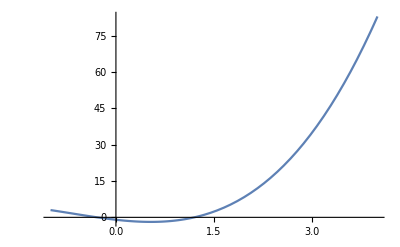

```mathematica
Clear[x,f,a,b,m,n,i]
f[x_]:=x^3+2 x^2-3x-1;
Plot[f[x],{x,-1,4}]
```

```mathematica
k=0.1; m=1;(*k = Subscript[p, o] and m = Subscript[p, 1]*)
n=6;
i=1;
p=m-f[m](m-k)/(f[m]-f[k]);(*k = Subscript[p, n-1] and m = Subscript[p, n]*)
OutputDetails={{i,p,f[p]}};
While[i<n,p=m-f[m](m-k)/(f[m]-f[k]);k=m;m=p;i++;OutputDetails=Append[OutputDetails,{i,p,f[p]}];]
(*Combining the output details with the headings of the table*)
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,{"i","p_i","f[p_i]"}}]],8]];
(*Printing Table*)
Print["Root After ",n," iterations ",NumberForm[N[p],8]]
(*8 is used to give the result with 8 digits precision*)
```

i | p_i | f[p_i]
1. | 4.2258065 | 97.499547
2. | 4.2258065 | 97.499547
3. | 1.0327495 | -0.86360442
4. | 1.0607837 | -0.73816727
5. | 1.2257585 | 0.16937497
6. | 1.1949692 | -0.022646757

Root After 6 iterations 1.1949692

Practical 4 - LU Decomposition

Ques 1:- Find the LU Decomposition of the matrix (1 | 2 | 3
1 | 4 | 9
1 | 8 | 27)

```mathematica
Clear [A,L,U,i,j]
A= {{1,2,3},{1,4,9},{1,8,27}}
{m,p,c}=LUDecomposition[A]
MatrixForm[m]
L=m SparseArray[{i_,j_}/;j<i->1,{3,3}]+IdentityMatrix[3];
U=m SparseArray[{i_,j_}/;j>=i->1,{3,3}];
MatrixForm /@{A,L,U,L.U}
A==L.U
```

{{1,2,3},{1,4,9},{1,8,27}}

{{{1,2,3},{1,2,6},{1,3,6}},{1,2,3},0}

(1 | 2 | 3
1 | 2 | 6
1 | 3 | 6)

{(1 | 2 | 3
1 | 4 | 9
1 | 8 | 27),(1 | 0 | 0
1 | 1 | 0
1 | 3 | 1),(1 | 2 | 3
0 | 2 | 6
0 | 0 | 6),(1 | 2 | 3
1 | 4 | 9
1 | 8 | 27)}

True

Ques 2: Find the LU decomposition of the matrix (1 | 2
3 | 4) and solve the system Ax = [4 (6])^T

```mathematica
Clear[A,L,U,i,j]
A= {{1,2},{3,4}}
{m,p,c}=LUDecomposition[A]
L=m SparseArray[{i_,j_}/;j<i->1,{2,2}]+IdentityMatrix[2];
U=m SparseArray[{i_,j_}/;j>=i->1,{2,2}];
MatrixForm/@{A,L,U,L.U}
A==L.U
X={{Subscript[x, 1]},{Subscript[x, 2]}};
B={{4},{6}}
Y={{Subscript[y, 1]},{Subscript[y, 2]}};
Subscript[Y, sol]=Solve[L.Y==B,{Subscript[y, 1],Subscript[y, 2]}]
Subscript[X, sol]=Solve[U.X==Y,{Subscript[x, 1],Subscript[x, 2]}]
Subscript[X, sol]/. Subscript[Y, sol]
```

{{1,2},{3,4}}

{{{1,2},{3,-2}},{1,2},0}

{(1 | 2
3 | 4),(1 | 0
3 | 1),(1 | 2
0 | -2),(1 | 2
3 | 4)}

True

{{4},{6}}

{{y_1→4,y_2→-6}}

{{x_1→y_1+y_2,x_2→-y_2/2}}

{{{x_1→-2,x_2→3}}}

Ques 3: Find the LU Decomposition of the matrix (2 | 7 | 5
6 | 20 | 10
4 | 3 | 0) and then solve the system Ax = [0 4 (1])^T

```mathematica
Clear [A,L,U,i,j]
A= {{2,7,5},{6,20,10},{4,3,0}}
{m,p,c}=LUDecomposition[A]
MatrixForm[m]
L=m SparseArray[{i_,j_}/;j<i->1,{3,3}]+IdentityMatrix[3];
U=m SparseArray[{i_,j_}/;j>=i->1,{3,3}];
MatrixForm /@{A,L,U,L.U}
A==L.U
X={{Subscript[x, 1]},{Subscript[x, 2]},{Subscript[x, 3]}};
B={{0},{4},{1}}
Y={{Subscript[y, 1]},{Subscript[y, 2]},{Subscript[y, 3]}};
Subscript[Y, sol]=Solve[L.Y==B,{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]}]
Subscript[X, sol]=Solve[U.X==Y,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]
Subscript[X, sol]/. Subscript[Y, sol]
```

{{2,7,5},{6,20,10},{4,3,0}}

{{{2,7,5},{3,-1,-5},{2,11,45}},{1,2,3},0}

(2 | 7 | 5
3 | -1 | -5
2 | 11 | 45)

{(2 | 7 | 5
6 | 20 | 10
4 | 3 | 0),(1 | 0 | 0
3 | 1 | 0
2 | 11 | 1),(2 | 7 | 5
0 | -1 | -5
0 | 0 | 45),(2 | 7 | 5
6 | 20 | 10
4 | 3 | 0)}

True

{{0},{4},{1}}

{{y_1→0,y_2→4,y_3→-43}}

{{x_1→1/6 (3 y_1+21 y_2+2 y_3),x_2→1/9 (-9 y_2-y_3),x_3→y_3/45}}

{{{x_1→-1/3,x_2→7/9,x_3→-43/45}}}

Practical 5 - GAUSS JACOBI METHOD

Ques 1:- Solve the system of equation by performing 15 iterations of Gauss Jacobi Iterative Method with initial approximation x_0 = [0,0,0]^T

5 x_1+ x_2+ 2 x_3=10
-3 x_1+9 x_2+4 x_3=-14
x_1 +2 x_2-7 x_3=-33

```mathematica
A={{5,1,2},{-3,9,4},{1,2,-7}};
b={{10},{-14},{-33}}
x0={{0},{0},{0}}
max=15
k=0
Size=Dimensions[A]
m=Size[[1]]
n=Size[[2]]
xk=x0 (*Subscript[x, k]*)
If[m!=n,Print["Not a square matrix, so we cannot proceed"],
OutputDetails={xk};
xk1=Table[0,{m}];(*Subscript[x, k+1]*)
While[k<max,For[i=1,i<=m,i++,xk1[[i]]=1/A[[i,i]](b[[i]]-∑_(j=1)^(i-1) A[[i,j]]*xk[[j]]-∑_(j=i+1)^m A[[i,j]]*xk[[j]]);];k++;
OutputDetails=Append[OutputDetails,xk1];xk=xk1;];
ColumnHeading=Table[x[j],{j,1,m}];]
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,ColumnHeading}]],8]]
```

{{10},{-14},{-33}}

{{0},{0},{0}}

15

0

{3,3}

3

3

{{0},{0},{0}}

x[1.] | x[2.] | x[3.]
0. | 0. | 0.
2. | -1.5555556 | 4.7142857
0.42539683 | -2.984127 | 4.5555556
0.77460317 | -3.438448 | 3.922449
1.11871 | -3.0406652 | 3.8425296
1.0711212 | -2.8904432 | 4.00534
0.97595265 | -2.9786663 | 4.0414621
0.9791484 | -3.0264434 | 4.00266
1.0042247 | -3.0081328 | 3.9894659
1.0058402 | -2.99391 | 3.9982799
0.99947004 | -2.9972888 | 4.0025743
0.99842803 | -3.0013208 | 4.0006989
0.99998459 | -3.0008346 | 3.9993981
1.0004077 | -2.9997376 | 3.9997593
1.0000438 | -2.9997571 | 4.0001332
0.99989814 | -3.0000446 | 4.0000756

PRACTICAL - 6 GAUSS SEIDEL METHOD

Ques. 2: Solve the system of equations by performing 10 iterations of the Gauss Seidel Iterative method with initial approximation x_0= [0,0,0]^T

```mathematica
A={{5,1,2},{-3,9,4},{1,2,-7}};
b={{10},{-14},{-33}}
x0={{0},{0},{0}}
max=15
k=0
Size=Dimensions[A]
m=Size[[1]]
n=Size[[2]]
xk=x0 (*Subscript[x, k]*)
If[m!=n,Print["Not a square matrix, so we cannot proceed"],
OutputDetails={xk};
xk1=Table[0,{m}];(*Subscript[x, k+1]*)
While[k<max,For[i=1,i<=m,i++,xk1[[i]]=1/A[[i,i]](b[[i]]-∑_(j=1)^(i-1) A[[i,j]]*xk1[[j]]-∑_(j=i+1)^m A[[i,j]]*xk[[j]]);];k++;
OutputDetails=Append[OutputDetails,xk1];xk=xk1;];
ColumnHeading=Table[x[j],{j,1,m}];]
Print[NumberForm[N[TableForm[OutputDetails,TableHeadings->{None,ColumnHeading}]],8]]
```

{{10},{-14},{-33}}

{{0},{0},{0}}

15

0

{3,3}

3

3

{{0},{0},{0}}

x[1.] | x[2.] | x[3.]
0. | 0. | 0.
2. | -0.88888889 | 4.7460317
0.27936508 | -3.5717813 | 3.7336861
1.2208818 | -2.808011 | 4.0864086
0.92703877 | -3.0627242 | 3.9716558
1.0238825 | -2.9794417 | 4.0092856
0.99217411 | -3.0067356 | 3.9969576
1.0025641 | -2.9977931 | 4.0009968
0.99915989 | -3.0007231 | 3.9996734
1.0002753 | -2.9997631 | 4.000107
0.99990981 | -3.0000776 | 3.9999649
1.0000295 | -2.9999746 | 4.0000115
0.99999032 | -3.0000083 | 3.9999962
1.0000032 | -2.9999973 | 4.0000012
0.99999896 | -3.0000009 | 3.9999996
1.0000003 | -2.9999997 | 4.0000001

PRACTICAL 7 - LAGRANGE INTERPOLATION

Ques. 1: Find Lagrange Interpolating polynomial for the following set of points: x_0=0, x_1=1, x_2=3, f(x_0)=1, f(x_1)=3, f(x_2)=55. And hence approximate the value of the function at the point x=2 using the resulting polynomial. Also plot the Lagrange polynomial and the points (x_i,f_i) on the same axes.

Langrange Polynomial = 1-6 x+8 x^2

21

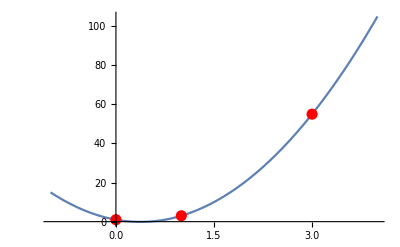

```mathematica
xi={0,1,3};
fi={1,3,55};
n=Length[xi];
m=Length[fi];
If[n!=m,Print["List of points and function values are not of same size"],For[i=1,i<=n,i++,L[i,x_]=(∏_(j=1)^(i-1) (x-xi[[j]])/(xi[[i]]-xi[[j]]))(∏_(j=i+1)^n (x-xi[[j]])/(xi[[i]]-xi[[j]]));];Polynomial[x_]=∑_(k=1)^n L[k,x]*fi[[k]];] 
Print["Langrange Polynomial = ",Simplify[Polynomial[x]]]
Polynomial[2]
A=Plot[Polynomial[x],{x,-1,4}];
B=Graphics[{Red,PointSize[0.02],Point[{0,1}],Point[{1,3}],Point[{3,55}]}];
Show[A,B]
```

Ques. 2: let f(x)=ln x. Find the Lagrange Interpolating polynomial for the following set of points: x_0=1, x_1=2, x_2=3, f(x_0)=ln 1, f(x_1)=ln 2, f(x_2)=ln 3. And hence approximate the value of the function at the point x=1.5 and x=2.4 using the resulting polynomial. Plot the function f(x) and the resulting Lagrange polynomial on the same axes over the range [1,3]. Next generate the plot of the difference between the Lagrange polynomial and the function f(x)= ln x

Langrange Polynomial = -0.980829+1.12467 x-0.143841 x^2

0.382534

0.889855

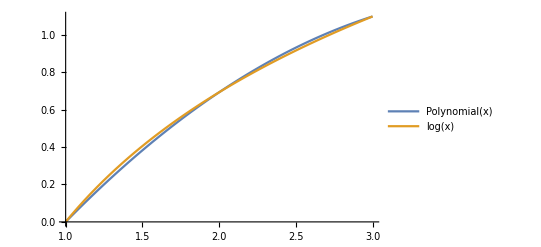

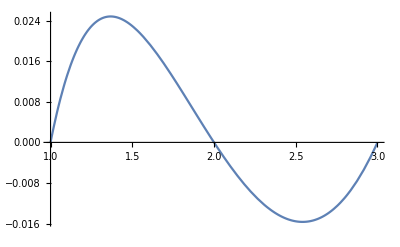

```mathematica
xi={1,2,3};
fi={N[Log[1]],N[Log[2]],N[Log[3]]};
n=Length[xi];
m=Length[fi];
If[n!=m,Print["List of points and function values are not of same size"],For[i=1,i<=n,i++,L[i,x_]=(∏_(j=1)^(i-1) (x-xi[[j]])/(xi[[i]]-xi[[j]]))(∏_(j=i+1)^n (x-xi[[j]])/(xi[[i]]-xi[[j]]));];Polynomial[x_]=∑_(k=1)^n L[k,x]*fi[[k]];] 
Print["Langrange Polynomial = ",Simplify[Polynomial[x]]]
Polynomial[1.5]
Polynomial[2.4]
Plot[{Polynomial[x],Log[x]},{x,1,3},PlotLegends->"Expressions"]
Plot[Log[x]-Polynomial[x],{x,1,3}]
```

Ques. 3: let f(x)=sin x. Find the Lagrange Interpolating polynomial for the following set of points: x_0=0, x_1= π/4, x_2= π/2, f(x_0)=sin 0, f(x_1)=sin π/4, f(x_2)=sin π/2. And hence approximate the value of the function at the point x=1.5 and x=2.4 using the resulting polynomial. Plot the function f(x) and the resulting Lagrange polynomial on the same axes over the range [0, π/2]. Next generate the plot of the difference between the Lagrange polynomial and the function f(x)= sin x

ClearAll

Langrange Polynomial = 0.+1.16401 x-0.335749 x^2

0.850762

0.517428

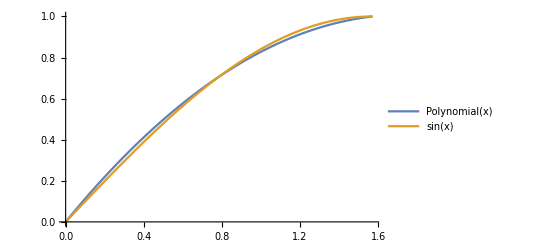

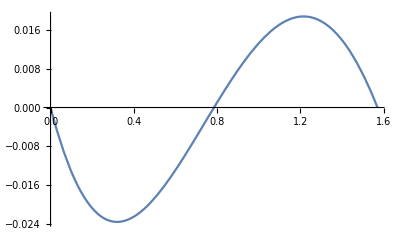

```mathematica
ClearAll
xi={0,π/4,π/2};
fi={N[Sin[0]],N[Sin[π/4]],N[Sin[π/2]]};
n=Length[xi];
m=Length[fi];
If[n!=m,Print["List of points and function values are not of same size"],For[i=1,i<=n,i++,L[i,x_]=(∏_(j=1)^(i-1) (x-xi[[j]])/(xi[[i]]-xi[[j]]))(∏_(j=i+1)^n (x-xi[[j]])/(xi[[i]]-xi[[j]]));];Polynomial[x_]=∑_(k=1)^n L[k,x]*fi[[k]];] 
Print["Langrange Polynomial = ",Simplify[Polynomial[x]]]
Polynomial[π/3]
Polynomial[π/6]
Plot[{Polynomial[x],Sin[x]},{x,0,π/2},PlotLegends->"Expressions"]
Plot[Sin[x]-Polynomial[x],{x,0,π/2}]
```

Ques. 4: let f(x) =e^x. Find the Lagrange Interpolating polynomial for the following set of points: x_0=-1, x_1= 0, x_2= 1, f(x_0)= e^-1, f(x_1)= e^0, f(x_2)= e^1. And hence approximate the value of the function at the point x= √e and x=e^(-1/3) using the resulting polynomial. Plot the function f(x) and the resulting Lagrange polynomial on the same axes over the range [-1,1]. Next generate the plot of the difference between the Lagrange polynomial and the function f(x)= e^x

```mathematica
ClearAll
xi={-1,0,1};
fi={N[Exp[-1]],N[Exp[0]],N[Exp[]]};
n=Length[xi];
m=Length[fi];
If[n!=m,Print["List of points and function values are not of same size"],For[i=1,i<=n,i++,L[i,x_]=(∏_(j=1)^(i-1) (x-xi[[j]])/(xi[[i]]-xi[[j]]))(∏_(j=i+1)^n (x-xi[[j]])/(xi[[i]]-xi[[j]]));];Polynomial[x_]=∑_(k=1)^n L[k,x]*fi[[k]];] 
Print["Langrange Polynomial = ",Simplify[Polynomial[x]]]
Polynomial[π/3]
Polynomial[π/6]
Plot[{Polynomial[x],Sin[x]},{x,0,π/2},PlotLegends->"Expressions"]
Plot[Sin[x]-Polynomial[x],{x,0,π/2}]
```

Practical 8 - Newton’s Interpolation

Ques 1: Find newtons form of interpolating polynomial for the following set of points: x_0 =0 , x_1 =1, x_2=3, f(x_0)=1, f(x_1)=3, f(x_2)=55. And hence approximate the value of the function at the point x=2 using the resulting polynomial Also find the divided difference f[x_1,x_2] , f[x_0,x_1] and f[x_0, x_1, x_2].

```mathematica
Polynomial = InterpolatingPolynomial[{{0,1},{1,3},{3,55}},x]
Simplify[Polynomial]
Polynomial /.x->2
xi={0,1,3};
fi={1,3,55};
f[x0,x1]=(fi[[2]]-fi[[1]])/(xi[[2]]-xi[[1]])
f[x1,x2]=(fi[[3]]-fi[[2]])/(xi[[3]]-xi[[2]])
f[x0,x1,x2]=(f[x1,x2]-f[x0,x1])/(xi[[3]]-xi[[1]])
```

1+(2+8 (-1+x)) x

1-6 x+8 x^2

21

2

26

8

Ques. 2: Find Newton’s form of Interpolating polynomial for the following set of points: x_0=-1, x_1=0, x_2=1, x_3=2, f(x_0)=5, f(x_1)=1, f(x_2)= 1, f(x_3)=11. And hence approximate the value of the function at the point x= 1.5 using the resulting polynomial. Also find the divided differences f[x_2, x_3] and f[x_1, x_2, x_3].

```mathematica
Polynomial = InterpolatingPolynomial[{{-1,5},{0,1},{1,1},{2,11}},x]
Simplify[Polynomial]
Polynomial /.x->1.5
xi={-1,0,1,2};
fi={5,1,1,11};
f[x0,x1]=(fi[[2]]-fi[[1]])/(xi[[2]]-xi[[1]])
f[x1,x2]=(fi[[3]]-fi[[2]])/(xi[[3]]-xi[[2]])
f[x2,x3]=(fi[[4]]-fi[[3]])/(xi[[4]]-xi[[3]])
f[x0,x1,x2]=(f[x1,x2]-f[x0,x1])/(xi[[3]]-xi[[1]])
f[x1,x2,x3]=(f[x2,x3]-f[x1,x2])/(xi[[4]]-xi[[2]])
f[x1,x2,x3]-f[x2,x3]
```

5+(1+x) (-4+x (1+x))

1-3 x+2 x^2+x^3

4.375

-4

0

10

2

5

-5

Practical 9 - Trapezoidal Rule

Ques.1 : Approximate the value of the integral ∫_1^2 1/x ⅆx using trapezoidal rule.

```mathematica
f[x_]:=1/x;
a=1;
b=2;
Exact=N[Integrate[f[x],{x,1,2}]]; (*exact value of integral*)
App=N[(b-a)/2(f[a]+f[b])];(*approximate value of integral*)
AE=Abs[Exact-App];(*actual error*)
Print["Exact value of integral is:-  ",Exact]
Print["Approximate value of the integral is:-  ",App]
Print["Actual Error is:-  ",AE]
```

Exact value of integral is:-  0.693147

Approximate value of the integral is:-  0.75

Actual Error is:-  0.0568528

Ques.2 : Approximate the value of the integral ∫_0^1 e^-x ⅆx using trapezoidal rule.

```mathematica
f[x_]:=Exp[-x];
a=0;
b=1;
Exact=N[Integrate[f[x],{x,0,1}]]; (*exact value of integral*)
App=N[(b-a)/2(f[a]+f[b])];(*approximate value of integral*)
AE=Abs[Exact-App];(*actual error*)
Print["Exact value of integral is:-  ",Exact]
Print["Approximate value of the integral is:-  ",App]
Print["Actual Error is:-  ",AE]
```

Exact value of integral is:-  0.632121

Approximate value of the integral is:-  0.68394

Actual Error is:-  0.0518192

Ques.3 : Approximate the value of the integral ∫_0^1 1/(1+x^2)ⅆx using trapezoidal rule.

```mathematica
f[x_]:=1/(1+x^2);
a=0;
b=1;
Exact=N[Integrate[f[x],{x,0,1}]]; (*exact value of integral*)
App=N[(b-a)/2(f[a]+f[b])];(*approximate value of integral*)
AE=Abs[Exact-App];(*actual error*)
Print["Exact value of integral is:-  ",Exact]
Print["Approximate value of the integral is:-  ",App]
Print["Actual Error is:-  ",AE]
```

Exact value of integral is:-  0.785398

Approximate value of the integral is:-  0.75

Actual Error is:-  0.0353982

Ques.4 : Approximate the value of the integral ∫_0^1 tan^-1 xⅆx using trapezoidal rule.

```mathematica
f[x_]:=ArcTan[x];
a=0;
b=1;
Exact=N[Integrate[f[x],{x,0,1}]]; (*exact value of integral*)
App=N[(b-a)/2(f[a]+f[b])];(*approximate value of integral*)
AE=Abs[Exact-App];(*actual error*)
Print["Exact value of integral is:-  ",Exact]
Print["Approximate value of the integral is:-  ",App]
Print["Actual Error is:-  ",AE]
```

Exact value of integral is:-  0.438825

Approximate value of the integral is:-  0.392699

Actual Error is:-  0.0461255

Practical 10 - Simpson’s Rule

Ques.1 : Approximate the value of the integral ∫_1^2 1/x ⅆx using simpson’s rule.

```mathematica
f[x_]:=1/x;
a=1;
b=2;
Exact=N[Integrate[f[x],{x,1,2}]]; (*exact value of integral*)
App=N[(b-a)/6(f[a]+4f[(a+b)/2]+f[b])];(*approximate value of integral*)
AE=Abs[Exact-App];(*actual error*)
Print["Exact value of integral is:-  ",Exact]
Print["Approximate value of the integral is:-  ",App]
Print["Actual Error is:-  ",AE]
```

Exact value of integral is:-  0.693147

Approximate value of the integral is:-  0.694444

Actual Error is:-  0.00129726

Ques.2 : Approximate the value of the integral ∫_0^1 e^-x ⅆx using simpson’s rule.

```mathematica
f[x_]:=Exp[-x];
a=0;
b=1;
Exact=N[Integrate[f[x],{x,0,1}]]; (*exact value of integral*)
App=N[(b-a)/6(f[a]+4f[(a+b)/2]+f[b])];(*approximate value of integral*)
AE=Abs[Exact-App];(*actual error*)
Print["Exact value of integral is:-  ",Exact]
Print["Approximate value of the integral is:-  ",App]
Print["Actual Error is:-  ",AE]
```

Exact value of integral is:-  0.632121

Approximate value of the integral is:-  0.632334

Actual Error is:-  0.000213121

Ques.3 : Approximate the value of the integral ∫_0^1 1/(1+x^2)ⅆx using simpson’s rule.

```mathematica
f[x_]:=1/(1+x^2);
a=0;
b=1;
Exact=N[Integrate[f[x],{x,0,1}]]; (*exact value of integral*)
App=N[(b-a)/6(f[a]+4f[(a+b)/2]+f[b])];(*approximate value of integral*)
AE=Abs[Exact-App];(*actual error*)
Print["Exact value of integral is:-  ",Exact]
Print["Approximate value of the integral is:-  ",App]
Print["Actual Error is:-  ",AE]
```

Exact value of integral is:-  0.785398

Approximate value of the integral is:-  0.783333

Actual Error is:-  0.00206483

Ques.4 : Approximate the value of the integral ∫_0^1 tan^-1 xⅆx using simpson’s rule.

```mathematica
f[x_]:=ArcTan[x];
a=0;
b=1;
Exact=N[Integrate[f[x],{x,0,1}]]; (*exact value of integral*)
App=N[(b-a)/6(f[a]+4f[(a+b)/2]+f[b])];(*approximate value of integral*)
AE=Abs[Exact-App];(*actual error*)
Print["Exact value of integral is:-  ",Exact]
Print["Approximate value of the integral is:-  ",App]
Print["Actual Error is:-  ",AE]
```

Exact value of integral is:-  0.438825

Approximate value of the integral is:-  0.439998

Actual Error is:-  0.00117353

Practical 11 - Eular’s Method

EULAR’S BLOCK

```mathematica
eular[f_,{x_,x0_,xn_},{y_,y0_},steps_]:=Block[{xold=x0,yold=y0,sollist={{x0,y0}},x,y,h},h=N[(xn-x0)/steps];Do[xnew=xold+h;ynew=yold+h*(f/.{x->xold,y->yold});sollist=Append[sollist,{xnew,ynew}];xold=xnew;yold=ynew,{steps}];Return[sollist]]
```

Ques 1: Approximate the solution of dy/dx=x+2y, with 0 ≤ x ≤ 1, y(0) =0 using four steps.

```mathematica
eular[x+2y,{x,0,1},{y,0},4]
```

{{0,0},{0.25,0.},{0.5,0.0625},{0.75,0.21875},{1.,0.515625}}

Ques 2: Approximate the solution of dy/dx=1+y/x, with 1 ≤ x ≤ 6, y(1) =1 using 10 steps.

```mathematica
eular[1+y/x,{x,1,6},{y,1},10]
```

{{1,1},{1.5,2.},{2.,3.16667},{2.5,4.45833},{3.,5.85},{3.5,7.325},{4.,8.87143},{4.5,10.4804},{5.,12.1448},{5.5,13.8593},{6.,15.6193}}

Ques 3: Approximate the solution of dy/dx=y/x, with 1 ≤ x ≤ 5, y(1) =1 using 10 steps.

```mathematica
eular[y/x,{x,1,5},{y,1},10]
```

{{1,1},{1.4,1.4},{1.8,1.8},{2.2,2.2},{2.6,2.6},{3.,3.},{3.4,3.4},{3.8,3.8},{4.2,4.2},{4.6,4.6},{5.,5.}}

Ques 4: Approximate the solution of dy/dx=xy^3-y, with 0 ≤ x ≤ 1, y(0) =1 using 4 steps.

```mathematica
eular[x y^3-y,{x,0,1},{y,1},4]
```

{{0,1},{0.25,0.75},{0.5,0.588867},{0.75,0.467175},{1.,0.369499}}

Practical 12 - Runge Kutta Method

RK4 BLOCK

```mathematica
RK4[f_,{x0_,xn_},y0_,steps_]:=Block[{xold=x0,yold=y0,sollist={{x0,y0}},x,y,n,h,k1,k2,k3,k4,fn,ynew,xnew},h=N[(xn-x0)/steps];Do[xnew=xold+h;k1=h*f[xold,yold];k2=h*f[xold+h/2,yold+k1/2];k3=h*f[xold+h/2,yold+k2/2];k4=h*f[xold+h,yold+k3];ynew=yold+1/6*(k1+2k2+2k3+k4);sollist=Append[sollist,{xnew,ynew}];xold=xnew;yold=ynew,{steps}];Return[sollist]]
```

Ques. 1:- Approximate the solution dy/dx=x+y, with 1≤x≤2, y(1)=1, using 10 steps.

```mathematica
f[x_,y_]:=x+y;
RK4[f,{1,2},1,10]
```

{{1,1},{1.1,1.21551},{1.2,1.46421},{1.3,1.74958},{1.4,2.07547},{1.5,2.44616},{1.6,2.86635},{1.7,3.34125},{1.8,3.87662},{1.9,4.4788},{2.,5.15484}}

Ques. 2:- Approximate the solution dy/dx=1+y/x, with 1≤x≤6, y(1)=1, using 5 steps.

```mathematica
f[x_,y_]:=1+y/x;
RK4[f,{1,6},1,5]
```

{{1,1},{2.,3.37963},{3.,6.285},{4.,9.53051},{5.,13.0288},{6.,16.7284}}

Ques. 3:- Approximate the solution dy/dx=x/y, with 0≤x≤5, y(0)=1, when h=0.5

```mathematica
f[x_,y_]:=x/y;
RK4[f,{0,5},1,10]
```

{{0,1},{0.5,1.11816},{1.,1.4144},{1.5,1.80294},{2.,2.2362},{2.5,2.69269},{3.,3.16237},{3.5,3.64014},{4.,4.12318},{4.5,4.60984},{5.,5.09908}}